Reproduction of Figure 1 of the Sniffers, buzzers, .... paper

Figures A

```mathematica
rateeqsA={v1->k0+k1 s, v2->k2 r};
parmA={k0->0.01,k1->1,k2->5};
v1sA[sv_]:=v1/.rateeqsA/.parmA/.s->sv
ssA=Solve[0==(v1-v2)/.rateeqsA,r][[1]];
ssnumA[sv_]:=r/.ssA/.parmA/.s->sv
pointA[sv_]:=Point[{ssnumA[sv],v1sA[sv]}]
```

```mathematica
plA1=Plot[{v1sA[1],v1sA[2],v1sA[3],v2/.rateeqsA/.parmA},{r,0,1},Frame->True,FrameLabel->{"R","rates, v_1 & v_2"},PlotStyle->{{Dashed,Black},{Dashed,Black},{Dashed,Black},{Black}},BaseStyle->{FontSize->14},Epilog->{Text["1",{0.8,1.2}],Text["2",{0.8,2.2}],Text["3",{0.8,3.2}],PointSize[0.025],pointA[1],pointA[2],pointA[3]},PlotRange->{0,6},AspectRatio->1];

plA2=Plot[r/.ssA/.parmA,{s,0,3},Frame->True,FrameLabel->{"S","R"},PlotStyle->Black,BaseStyle->{FontSize->14},PlotRange->{0,0.7},Epilog->{Text["Linear",{1.5,0.65}]},AspectRatio->1];
```

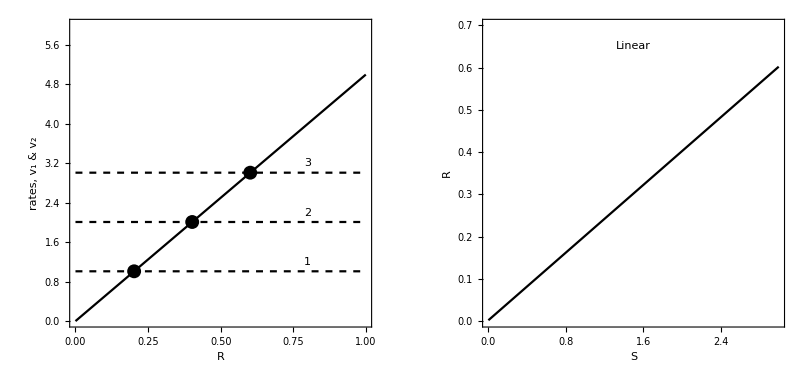

```mathematica
GraphicsGrid[{{plA1,plA2}}]
```

Figures B

```mathematica
rateeqsB={v1->k1 s (rt-rp), v2->k2 rp};
parmB={k1->1,k2->1,rt->1};
v1sB[sv_]:=v1/.rateeqsB/.parmB/.s->sv
ssB=Solve[0==(v1-v2)/.rateeqsB,rp][[1]];
ssnumB[sv_]:=rp/.ssB/.parmB/.s->sv
pointB[sv_]:=Point[{ssnumB[sv],v1/.rateeqsB/.parmB/.s->sv/.rp->ssnumB[sv]}]
```

```mathematica
plB1=Plot[{v1sB[2],v1sB[4],v1sB[8],v2/.rateeqsB/.parmB},{rp,0,1},Frame->True,FrameLabel->{"RP","rates, v_1 & v_2"},PlotStyle->{{Dashed,Black},{Dashed,Black},{Dashed,Black},{Black}},BaseStyle->{FontSize->14},Epilog->{Text["2",{0.3,1.6}],Text["4",{0.675,1.6}],Text["8",{0.9,1.6}],PointSize[0.035],pointB[2],pointB[4],pointB[8]},PlotRange->{0,2},AspectRatio->1];

plB2=Plot[rp/.ssB/.parmB,{s,0,10},Frame->True,FrameLabel->{"S","R"},PlotStyle->Black,BaseStyle->{FontSize->14},PlotRange->{0,1.1},Epilog->{Text["Hyperbolic",{5,1}]},AspectRatio->1];
```

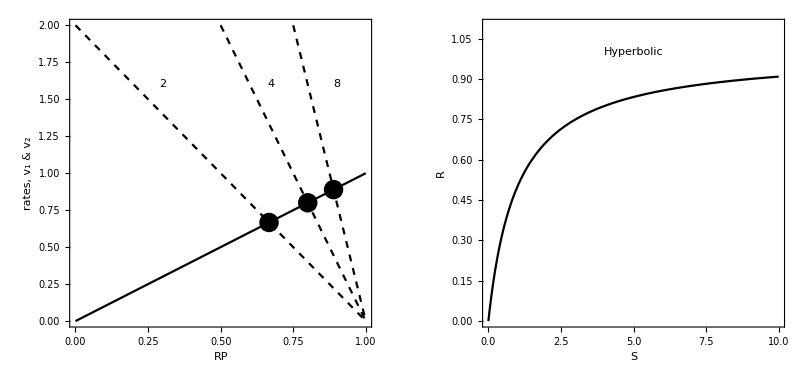

```mathematica
GraphicsGrid[{{plB1,plB2}}]
```

Figures C

```mathematica
rateeqsC={v1->(k1 s (rt-rp))/(Km1+rt-rp), v2->k2 rp/(Km2+rp)};
parmC={k1->1,k2->1,rt->1,Km1->0.05,Km2->0.05};
v1sC[sv_]:=v1/.rateeqsC/.parmC/.s->sv
ssC=Solve[0==(v1-v2)/.rateeqsC,rp][[2]];
ssnumC[sv_]:=rp/.ssC/.parmC/.s->sv
pointC[sv_]:=Point[{ssnumC[sv],v1/.rateeqsC/.parmC/.s->sv/.rp->ssnumC[sv]}]
```

```mathematica
plC1=Plot[{v1sC[0.25],v1sC[0.5],v1sC[1],v1sC[1.5],v1sC[2],v2/.rateeqsC/.parmC},{rp,0,1},Frame->True,FrameLabel->{"RP","rates, v_1 & v_2"},PlotStyle->{{Dashed,Black},{Dashed,Black},{Dashed,Black},{Dashed,Black},{Dashed,Black},{Black}},BaseStyle->{FontSize->14},Epilog->{Text["0.25",{0.25,0.25}],Text["0.5",{0.25,0.5}],Text["1",{0.25,1}],Text["1.5",{0.25,1.5}],Text["2",{0.7,1.85}],PointSize[0.035],pointC[0.25],pointC[0.5],pointC[1.01],pointC[1.5],pointC[2]},PlotRange->{0,2},AspectRatio->1];

plC2=Plot[rp/.ssC/.parmC,{s,0,3},Frame->True,FrameLabel->{"S","RP"},PlotStyle->Black,BaseStyle->{FontSize->14},PlotRange->{0,1.1},Epilog->{Text["Sigmoidal",{1.5,1}]},AspectRatio->1];
```

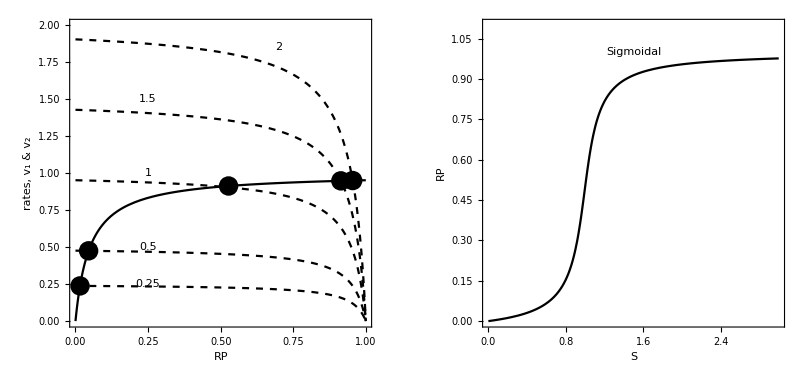

```mathematica
GraphicsGrid[{{plC1,plC2}}]
```

Figure D

```mathematica
rateeqsD={v1->k1 s,v2->k2 x r}/.x->(k3 s)/k4;
parmD={k1->2,k2->2,k3->1,k4->1};
v1sD[sv_]:=v1/.rateeqsD/.parmD/.s->sv
v2sD[sv_]:=v2/.rateeqsD/.parmD/.s->sv
ssD=Solve[0==(v1-v2)/.rateeqsD,r][[1]];
pointD[sv_]:=Point[{r/.ssD/.parmD,v1/.rateeqsD/.parmD/.s->sv}]

odesD={
r'[t]==v1-v2,
x'[t]==v3-v4};
ratesD={v1->k1 s[t],v2->k2 x[t] r[t],v3->k3 s[t],v4->k4 x[t]};
initcondD={r[0]==(k1 k4)/(k2 k3),x[0]==(k3 s)/k4}/.parmD;
```

```mathematica
s[t_]:=0/;t<4
s[t_]:=1/;4≤t≤ 8
s[t_]:=2/;8≤t≤ 12
s[t_]:=3/;12≤t≤ 16
s[t_]:=4/;16≤t≤ 20
tsolD=
NDSolve[Join[odesD/.ratesD/.parmD,initcondD/.parmD/.s->0],{r,x},{t,0,20}];
```

```mathematica
plD1=Plot[{v1sD[1],v2sD[1],v1sD[2],v2sD[2],v1sD[3],v2sD[3]},{r,0,2},Frame->True,FrameLabel->{"R","rates, v_1 & v_2"},BaseStyle->{FontSize->14},PlotRange->{0,8},AspectRatio->1,PlotStyle->{{Dashed,Red},{Red},{Dashed,Blue},{Blue},{Dashed,Green},{Green}},Epilog->{Red,Text["1",{1.4,2.25}],Blue,Text["2",{1.25,4.25}],Green,Text["3",{1.15,6.25}],Black,PointSize[0.025],pointD[1],pointD[2],pointD[3]}];

plD2=Plot[{x[t]/.tsolD,s[t],r[t]/.tsolD},{t,0,20},Frame->True,FrameLabel->{"time","r, s, x"},BaseStyle->{FontSize->14},PlotRange->{0,5},AspectRatio->1,Epilog->{Text["Adapted",{10,4.75}],Text["R",{5,1.9}],Red,Text["S",{15.5,3.8}],Green,Text["X",{14.7,2.7}]},PlotStyle->{Green,Red,Black}];
```

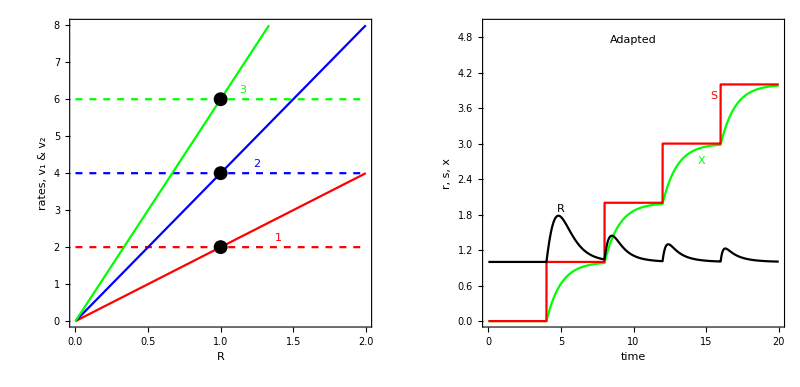

```mathematica
GraphicsGrid[{{plD1,plD2}}]
```

Figure E

```mathematica
G[u_,v_,J_,K_]:=(2*u*K)/(v-u+v*J+u*K+√((v-u+v*J+u*K)^2-4*(v-u)*u*K))
```

```mathematica
rateeqsE={
v1->ko G[k3 r[t],k4,J3,J4] + k1 s,
v2->k2 r[t]};
parmE={
ko->0.4,k1->0.01,k2->1,k3->1,k4->0.2,J3->0.05,J4->0.01};
v1sE[sv_]:=v1/.rateeqsE/.parmE/.s->sv
```

```mathematica
plE1=Plot[{
v1sE[0],v1sE[8],v1sE[16],v2/.rateeqsE/.parmE},{r[t],0,0.75},PlotRange->{0,0.6},Frame->True,FrameLabel->{"R","rates, v_1 & v_2"},BaseStyle->{FontSize->14},PlotRange->{0,8},AspectRatio->1,PlotStyle->{{Dashed,Black},{Dashed,Black},{Dashed,Black},{Black}},Epilog->{Text["0",{0.7,0.4}],Text["8",{0.7,0.49}],Text["16",{0.7,0.57}]}];
```

```mathematica
rss=Solve[0==(v1-v2)/.rateeqsE,s][[1]][[1]][[2]];
dataE=Table[{rss/.parmE,r[t]},{r[t],0,1,0.005}];
```

```mathematica
plE2=ListLinePlot[dataE,PlotRange->{{0,20},{0,0.7}},Frame->True,FrameLabel->{"S","R"},BaseStyle->{FontSize->14},AspectRatio->1,PlotStyle->Black,Epilog->{Text["Mutual activation",{10,0.65}],Arrow[{{15.5,0.25},{15.5,0.19}}],Text["S_crit",{15.5,0.28}]}];
```

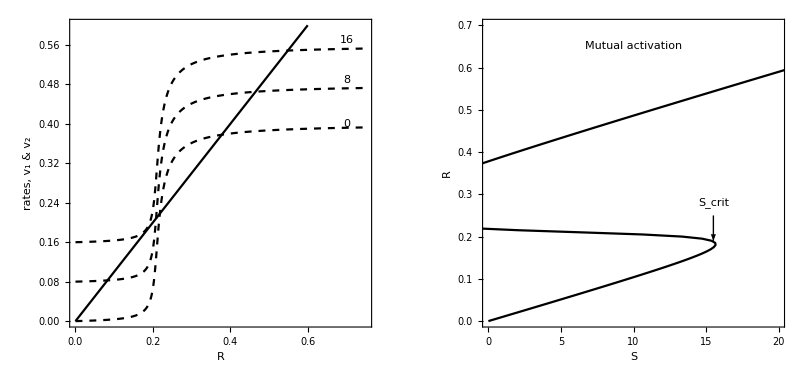

```mathematica
GraphicsGrid[{{plE1,plE2}}]
```

Figure 1F

```mathematica
rateeqsF =  {v1 -> k0 + k1 s,
v2 -> (k2 r + k2b e r /.e-> G[k3 , k4 r, J3, J4]) };
parmF=  {k0 -> 0, k1 -> 0.05, k2-> 0.1,k2b-> 0.5, k3-> 1,k4 -> 0.2,J3 -> 0.05, J4 -> 0.05};
```

```mathematica
plF1=Plot[{v2/.rateeqsF/.parmF,0.6,1.5,2.5},{r,0,25},Frame->True,FrameLabel->{"R","rates, v_1 & v_2"},BaseStyle->{FontSize->14},PlotRange->{0,3},AspectRatio->1,PlotStyle->{Black,{Dashed,Black},{Dashed,Black},{Dashed,Black}},
Epilog->{Text["0.6",{20,0.7}],Text["1.5",{20,1.6}],Text["2.5",{20,2.6}]}];
```

```mathematica
ssF=s/.Solve[0==(v1-v2)/.rateeqsF/.parmF,s][[1]];
dataF=Table[{ssF,r},{r,0,20,0.02}];
plF2=ListLinePlot[%,Frame->True,FrameLabel->{"R","rates, v_1 & v_2"},BaseStyle->{FontSize->14},PlotRange->{{0,50},{0,20}},AspectRatio->1,PlotStyle->Black,Epilog->{Text["Mutual inhibition",{25,19}],Arrow[{{42.5,7},{42.5,4.6}}],Text["S_crit",{42.5,7.5}],Arrow[{{21.2,10},{21.2,8}}],Text["S_crit",{21.2,10.5}]}];
```

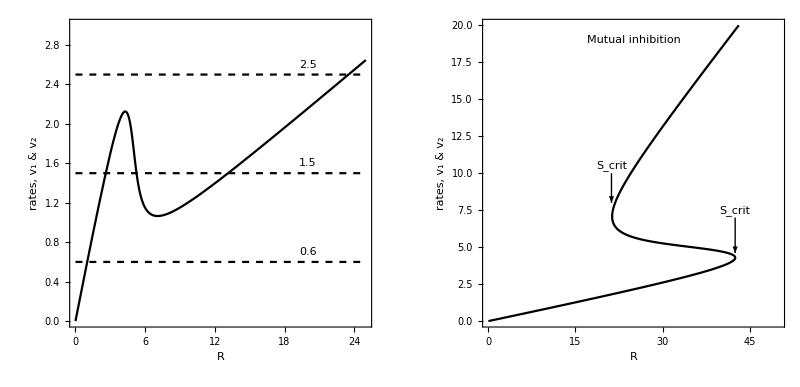

```mathematica
GraphicsGrid[{{plF1,plF2}}]
```

Figure G

```mathematica
rateeqsG={v1 -> (k0 e/. e -> G[k3, k4 r, J3,J4]),v2 -> k2 s r };
parmsG={k0 -> 1, k2 -> 1, k3-> 0.5, k4-> 1, J3-> 0.001, J4-> 0.001};
```

```mathematica
ssG[sv_]:=Solve[0==(v1-v2)/.rateeqsG/.parmsG/.s->sv,r][[1]]
```

```mathematica
pointG[sv_]:=Point[{r/.ssG[sv],v1/.rateeqsG/.parmsG/.ssG[sv]}]
```

```mathematica
plG1=Plot[Evaluate[{v1,v2}/.(rateeqsG/.parmsG)/.s->{0.5,1,1.5}],{r,0,1},PlotStyle -> {{Black,Dashed},Black,Black,Black},Frame->True,FrameLabel->{"R","rates, v_1 & v_2"},BaseStyle->{FontSize->14},PlotRange->{0,1.2},AspectRatio->1,Epilog->{PointSize[0.02],pointG[0.5],pointG[1],pointG[1.5],Text["0.5",{0.9,0.5}],Text["1",{0.9,0.95}],Text["1.5",{0.675,1.1}]}];
```

```mathematica
plG2=ListLinePlot[Table[{s,r/.ssG[s]},{s,0.001,2,0.01}],PlotStyle -> Black,Frame->True,FrameLabel->{"S","R"},BaseStyle->{FontSize->14},PlotRange->{{0,2},{0,1}},AspectRatio->1,Epilog->{Text["Homeostatic",{1,0.9}]}];
```

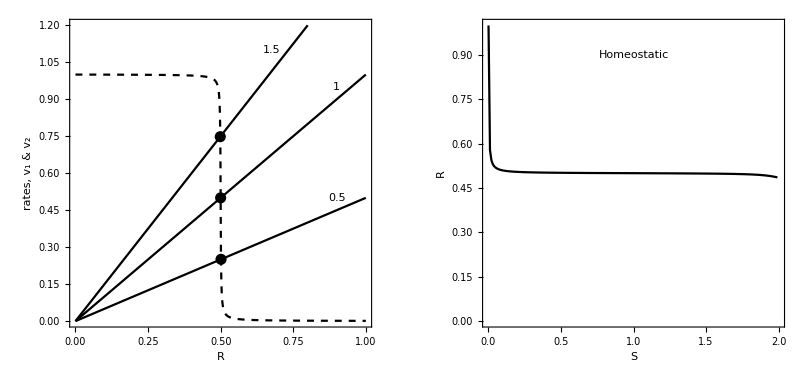

```mathematica
GraphicsGrid[{{plG1,plG2}}]
```

All plots

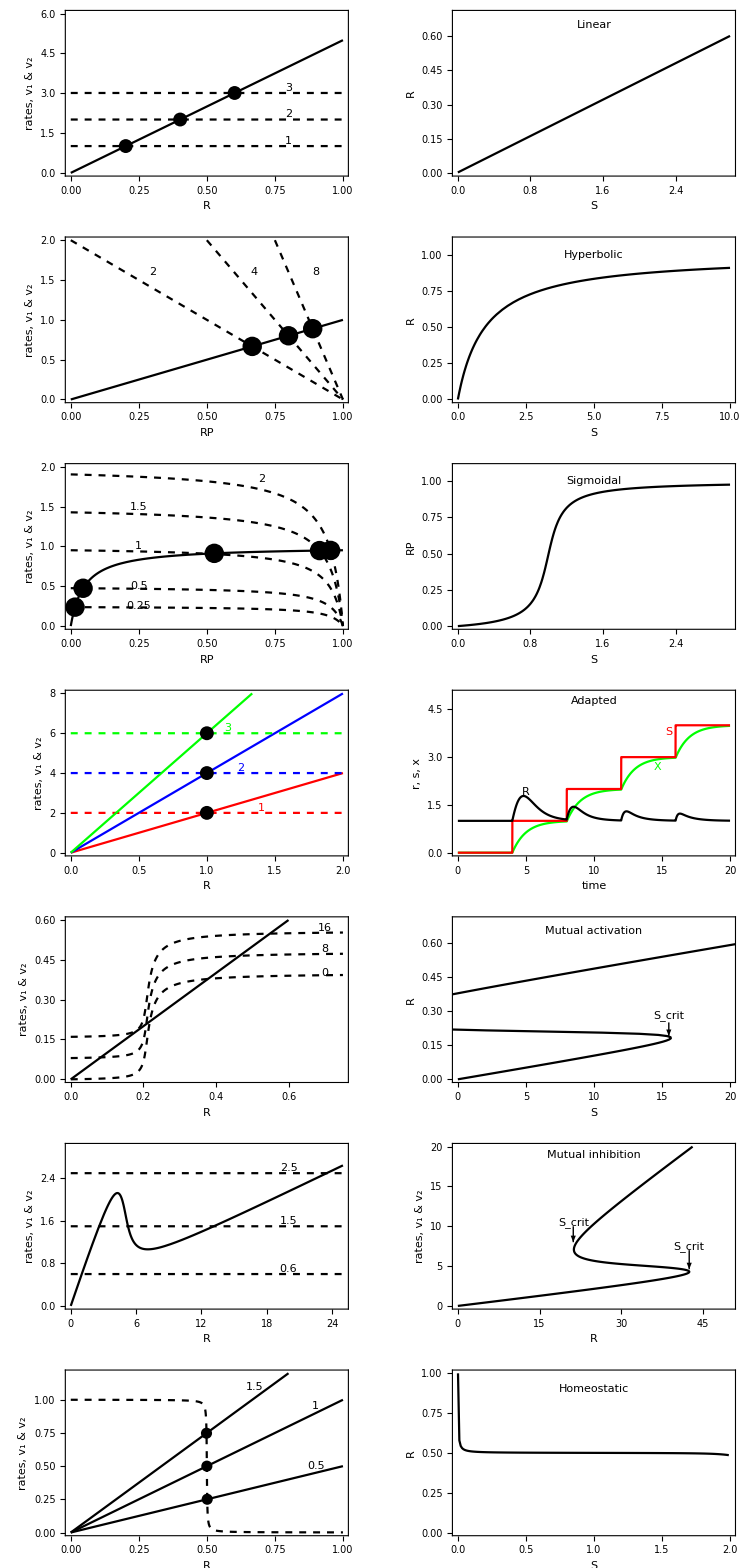

```mathematica
GraphicsGrid[
{
{plA1,plA2},
{plB1,plB2},
{plC1,plC2},
{plD1,plD2},
{plE1,plE2},
{plF1,plF2},
{plG1,plG2}
},ImageSize->750]
```